Your Title Here

```mathematica
L1=10;L2=7/12*L1;θ=30°;
```

```mathematica
w1=0.5*L1;w2=L1*Cos[θ];
```

```mathematica
h1=1.2*L1;h2=0.3*h1;
```

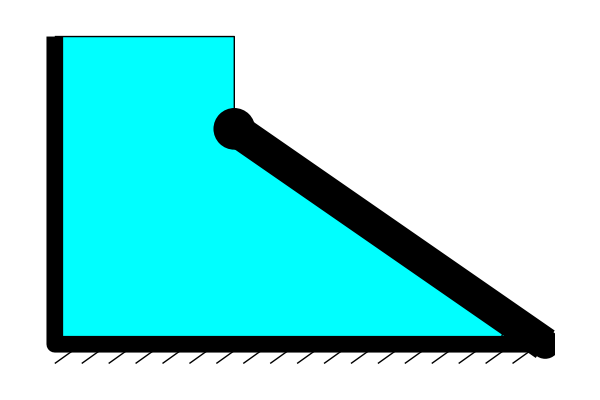

```mathematica
Module[{},


Graphics[{
{Cyan,Polygon[{{w1,h1},{0,h1},{0,0},{w1+w2,0},{w1,h1-h2}}]},

{Thickness@0.02,CapForm@None,Line[{{0,h1},{0,0},{w1+w2,0}}]},
{Thick,Line[{{0,h1},{w1,h1},{w1,h1-h2}}]},
{Thickness@0.04,CapForm@None,Line[{{w1,h1-h2},{w1+w2,0}}]},
{PointSize@0.035,Point@{w1+w2,0},PointSize@0.05,Point@{w1,h1-h2}},

Circle[{w1+w2,0},1.25,{180°,165°-θ}],
Text[Style["θ",Italic,17],{w1+w2,0},{7.5,-1.2}],

Line[{{#,-0.75},{#+0.75,0}}]&/@Range[0,w1+w2-0.75,0.75],

(*{Red,PointSize@0.02,Point@{w1+L2*Cos[θ],h1-h2-L2*Sin[θ]}}*)
},ImageSize->{600,400}]
]
```

```mathematica
labels=Graphics[{
Line[{{0,-δ},{w1,-δ}}],Line[{{#,-0.8*δ},{#,-1.12*δ}}]&/@{0,w1},
Text[Style[Subscript[Style["w",Italic],1],17,Background->White],{0.5*w1,-δ}],

Line[{{w1,-δ},{w1+w2,-δ}}],Line[{{#,-0.8*δ},{#,-1.2*δ}}]&/@{w1,w1+w2},
Text[Style[Subscript[Style["w",Italic],2],17,Background->White],{w1+0.5*w2,-δ}],

Line[{{-δ,0},{-δ,h1}}],Line[{{-0.8*δ,#},{-1.2*δ,#}}]&/@{0,h1},
Text[Style[Subscript[Style["h",Italic],1],17,Background->White],{-δ,0.5*h1}],

Line[{{w1+δ,h2},{w1+δ,h1}}],Line[{{w1+0.8*δ,#},{w1+1.2*δ,#}}]&/@{h2,h1},
Text[Style[Subscript[Style["h",Italic],2],17,Background->White],{w1+δ,h2+0.5*(h1-h2)}]
}];
```

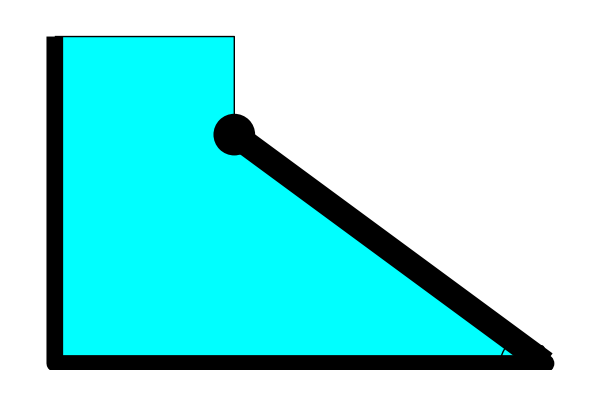





```mathematica
Module[{δ,L,θ,w1,w2,h1,h2,gate,labels},
δ=1;
L=10;θ=30°;
w1=0.5*L;w2=L*Cos[θ];
h1=1.2*L;h2=0.7*h1;

gate=Graphics[{
{Cyan,Polygon[{{w1,h1},{0,h1},{0,0},{w1+w2,0},{w1,h2}}]},

{Thickness@0.02,CapForm@None,Line[{{0,h1},{0,0},{w1+w2,0}}]},
{Thick,Line[{{0,h1},{w1,h1},{w1,h2}}]},
{Thickness@0.03,CapForm@None,Line[{{w1,h2},{w1+w2,0}}]},
{PointSize@0.022,Point@{w1+w2,0},PointSize@0.05,Point@{w1,h2}},

Circle[{w1+w2,0},1.25,{180°,165°-θ}],
Text[Style["θ",Italic,17],{w1+w2,0},{7.5,-1.2}]
},ImageSize->{600,400}]
]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX